```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={γ∈Reals, β∈Reals, ω ∈Reals}
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

{γ∈ℝ,β∈ℝ,ω∈ℝ}

1

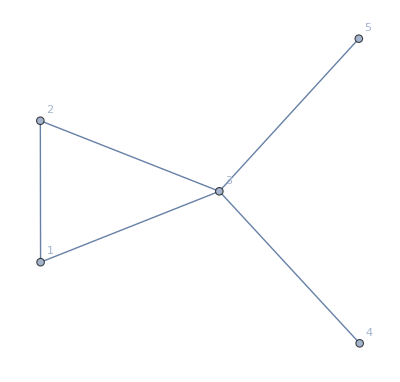

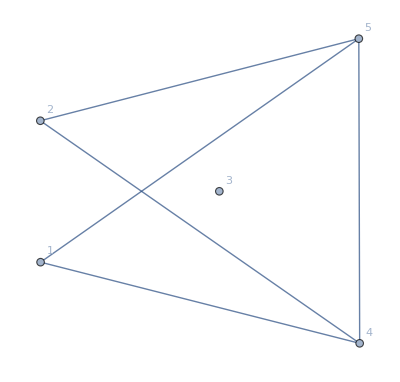

```mathematica
ω =2;
shots=1000;
p = 1
G = Graph[{1<->2, 2<->3,  1<->3,  4<->3,  5<->3}, VertexLabels->"Name"]
Gcomp = GraphComplement[G]
```

```mathematica
nVertices = VertexCount[G];
mult[operator_,totalQubits_]:= If[totalQubits > 0, Nest[KroneckerProduct[#,operator]&,operator,totalQubits-1], Unevaluated[Sequence[]]] ;
matExp[operator_, angle_]:= Cos[angle]*IdentityMatrix[2^nVertices] - I *Sin[angle]*operator
compGham[edge_]:= Z[[edge[[1]]]].Z[[edge[[2]]]]- Z[[edge[[1]]]] - Z[[edge[[2]]]]
X = Table[KroneckerProduct[mult[IdentityMatrix[2], j-1], PauliMatrix[1], mult[IdentityMatrix[2], nVertices-j]],{j,nVertices}];
Z = Table[KroneckerProduct[mult[IdentityMatrix[2], j-1], PauliMatrix[3], mult[IdentityMatrix[2], nVertices-j]],{j,nVertices}];
γs = Table[Symbol["γ"<>ToString@i],{i,p}];
βs =Table[Symbol["β"<>ToString@i],{i,p}];
AllStates=Module[{temp},Table[temp=ConstantArray[0,2^ nVertices];
temp[[j]]=1; temp, {j,1,2^nVertices}]];
```

#### H= - sum (1-Z)/2 + w/4 sum(1-Z)(1-Z) -> sum Z/2 + w/4 sum(ZZ - Z - Z)

```mathematica
H0 = Total[Z]/2;
GcompEdges = EdgeList[Gcomp]
H1 = ω/4*Sum[compGham[GcompEdges[[j]]], {j, Length[GcompEdges]}];
H = H0 +H1;
expX = Table[Table[matExp[X[[j]], βs[[i]]],{j, nVertices}],{i, p}];
negExpX =  Table[Table[matExp[X[[j]], -βs[[i]]],{j, nVertices}],{i, p}];
expH = Table[MatrixExp[-ⅈ γs[[j]] * H], {j,p}];
expB= Table[ParallelCombine[Dot[Sequence@@##]&,expX[[j]],Dot], {j,p}];

UDagger= Table[MatrixExp[ⅈ γs[[j]] * H], {j,p}];
BDagger =  Table[ParallelCombine[Dot[Sequence@@##]&,negExpX[[j]],Dot], {j,p}];
```

{1<->4,1<->5,2<->4,2<->5,4<->5}

```mathematica
initialState = ConstantArray[0,2^nVertices];
initialState[[1]] = 1;
Hadamard = mult[1/Sqrt[2]*{{1,1}, {1,-1}}, nVertices];
state = Hadamard.initialState;
matrixList = Table[expB[[j]].expH[[j]], {j, p, 1, -1}];
final= Apply[Dot, matrixList].state;
finalBra = state.UDagger[[1]].BDagger[[1]];
expectation = finalBra.H.final;
```

```mathematica
plotData=Table[{γ1, β1, Re[expectation//Simplify]}, {γ1,0,π,0.1}, {β1,0,π,0.1}];
```

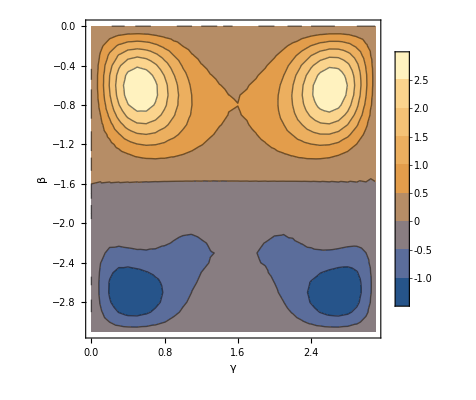

```mathematica
If[p == 1,  ListContourPlot[Flatten[ plotData,1], AxesLabel->{ γ,β}, PlotRange->All,PlotLegends->Automatic,ScalingFunctions->{Automatic,"Reverse"}]]
```

```mathematica
meanEnergy =Module[{samples, probabilities, energy}, Table[probabilities= N[Conjugate[final] * final];
samples=RandomVariate[MultinomialDistribution[shots,Re[probabilities ]]];
energy=Tr[Table[samples[[j]]AllStates[[j]].H.AllStates[[j]]/shots // N, {j,1,2^nVertices}]];
{γ1, β1,energy}, {γ1,0,π,0.1}, {β1,0,π,0.1}]];
```

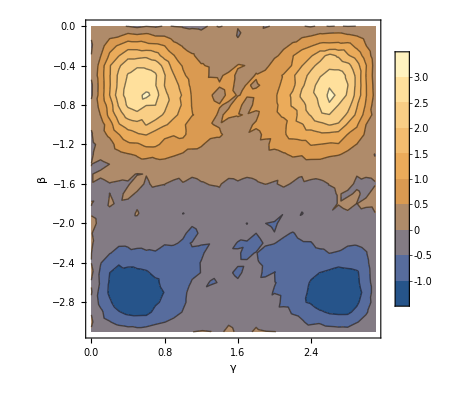

```mathematica
If[p == 1,  ListContourPlot[Flatten[ meanEnergy,1], AxesLabel->{ γ,β}, PlotRange->All,PlotLegends->Automatic,ScalingFunctions->{Automatic,"Reverse"}]]
```